```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsNEW=ReadList[FileNameJoin[{Directory[],"files/PureIntegralBasis1-138.txt"}]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
```

```mathematica
PureIntegralsNEW[[139;;]]//Length
ReduListT=PureIntegralsNEW[[139;;]]/.hxb[n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_,n12_,n13_]:>{n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13};
Sectors=ReduListT/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) //DeleteDuplicates;
Sectors2=ReduListT/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) ;
RemainingSectors=SortBy[Tally[Sectors2],Last]
RemainingSectors//Length
```

103

{{{0,1,0,1,1,1,1,1,1,0,0,0,0},1},{{0,1,1,1,0,1,1,1,1,0,0,0,0},1},{{1,0,1,1,0,0,1,1,1,0,0,0,0},1},{{1,0,1,1,0,1,0,1,1,0,0,0,0},1},{{1,0,1,1,0,1,1,1,1,0,0,0,0},1},{{1,0,1,1,1,0,1,1,0,0,0,0,0},1},{{1,0,1,1,1,1,0,1,0,0,0,0,0},1},{{1,0,1,1,1,1,1,1,0,0,0,0,0},1},{{1,1,0,1,1,1,1,1,0,0,0,0,0},1},{{1,1,1,1,1,1,1,1,1,0,0,0,0},1},{{0,0,1,1,0,1,1,1,1,0,0,0,0},2},{{0,1,0,1,0,1,1,1,1,0,0,0,0},2},{{0,1,0,1,1,0,1,1,1,0,0,0,0},2},{{0,1,0,1,1,1,0,1,1,0,0,0,0},2},{{0,1,0,1,1,1,1,1,0,0,0,0,0},2},{{0,1,1,1,0,0,1,1,0,0,0,0,0},2},{{0,1,1,1,0,0,1,1,1,0,0,0,0},2},{{0,1,1,1,0,1,0,1,0,0,0,0,0},2},{{0,1,1,1,0,1,0,1,1,0,0,0,0},2},{{0,1,1,1,0,1,1,1,0,0,0,0,0},2},{{1,0,0,1,1,1,1,1,0,0,0,0,0},2},{{1,1,0,1,0,1,0,1,0,0,0,0,0},2},{{1,1,0,1,0,1,1,1,0,0,0,0,0},2},{{1,1,0,1,1,0,1,1,0,0,0,0,0},2},{{1,1,0,1,1,1,0,1,0,0,0,0,0},2},{{1,1,1,1,0,1,1,1,1,0,0,0,0},3},{{1,1,1,1,1,0,1,1,1,0,0,0,0},3},{{1,1,1,1,1,1,0,1,0,0,0,0,0},3},{{1,1,1,1,1,1,0,1,1,0,0,0,0},3},{{1,1,1,1,1,1,1,1,0,0,0,0,0},3},{{1,1,1,1,0,0,1,1,1,0,0,0,0},4},{{1,1,1,1,0,1,0,1,1,0,0,0,0},4},{{1,1,1,1,1,0,1,1,0,0,0,0,0},4},{{1,1,1,1,0,0,1,1,0,0,0,0,0},5},{{1,0,1,1,0,0,1,1,0,0,0,0,0},6},{{1,0,1,1,0,1,0,1,0,0,0,0,0},6},{{1,0,1,1,0,1,1,1,0,0,0,0,0},6},{{1,1,1,1,0,1,0,1,0,0,0,0,0},6},{{1,1,1,1,0,1,1,1,0,0,0,0,0},7}}

39

```mathematica
Position[Sectors2/.{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_,n12_,n13_}:>hxb[n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13],RemainingSectors[[19,1]]/.List->hxb]+119
```

{{123},{141}}

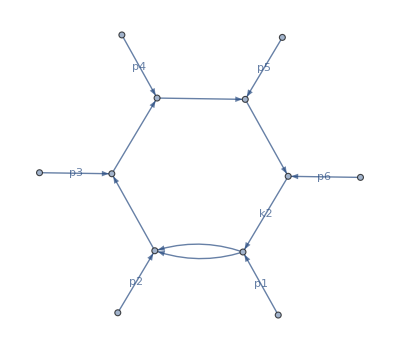
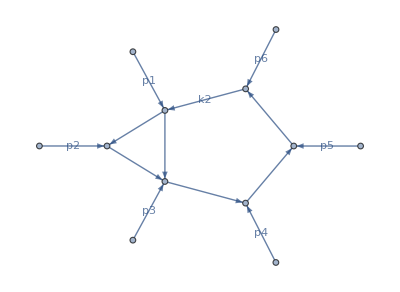
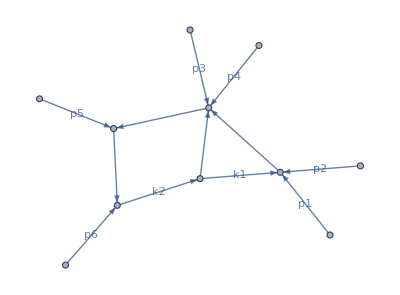
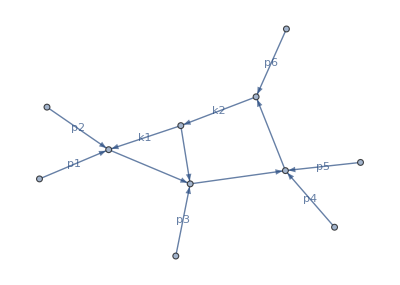
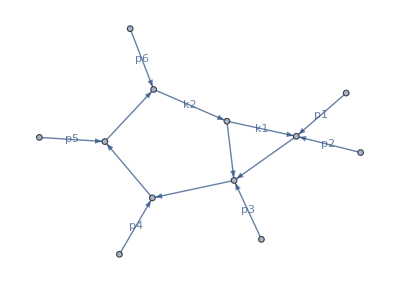
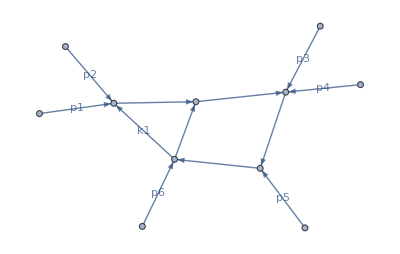
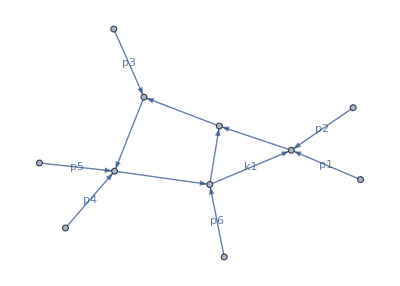
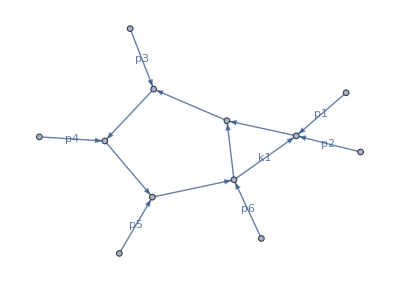
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 0

```mathematica
PlotDiagrams=Table[plotDiagram[RemainingSectors[[i,1]]],{i,1,Length[RemainingSectors]}];
Grid[ArrayReshape[PlotDiagrams,{8,5}]]
```

```mathematica
17*3
```

51

```mathematica
RemSubBubbles={11,12,13,14,15,21,1};
ArrayReshape[RemainingSectors[[RemSubBubbles]][[All,2]],{4,2}]//MatrixForm
Grid[ArrayReshape[PlotDiagrams[[RemSubBubbles]],{4,2}]]
```

(2 | 2
2 | 2
2 | 2
1 | 0)

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | 0

```mathematica
Form=Thread[Total[Transpose[RemainingSectors[[RemSubBubbles]][[All,1]]]]]-1;
Permutation=FindPermutation[Form,Sort[Form]]
ResumBubbles2=Permute[RemSubBubbles,Permutation]
ArrayReshape[RemainingSectors[[ResumBubbles2]][[All,2]],{4,2}]//MatrixForm
Grid[ArrayReshape[PlotDiagrams[[ResumBubbles2]],{4,2}]]
```

Cycles[{}]

{11,12,13,14,15,21,1}

(2 | 2
2 | 2
2 | 2
1 | 0)

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | 0

```mathematica
RemainingSectors[[ResumBubbles2]][[All,1]]
```

{{0,0,1,1,0,1,1,1,1,0,0,0,0},{0,1,0,1,0,1,1,1,1,0,0,0,0},{0,1,0,1,1,0,1,1,1,0,0,0,0},{0,1,0,1,1,1,0,1,1,0,0,0,0},{0,1,0,1,1,1,1,1,0,0,0,0,0},{1,0,0,1,1,1,1,1,0,0,0,0,0},{0,1,0,1,1,1,1,1,1,0,0,0,0}}

```mathematica
Length[RemainingSectors]
```